## 2WF34 Mathematica Practicum 7 exercises

This series of notebooks is made in Mathematica 12.2

Contact: Jan Willem Knopper, MF 6.095/MF 5.121 j.w.knopper@tue.nl
Author: Jan Willem Knopper, based on the optional assignment from Martijn Anthonissen.

## 7. Final exercise (due 30 March 23:55)

### Introduction

Some links can be found in the slide section for this week (see the assignment description for links) .
  This file contains a copy of the necessary parts from the Mathematica notebook, since for some versions these need to be executed in the same notebook . The other code in the other notebook can be useful as well .
  
  The resources for this assignment contain: A this exercise file, B1 the YouTube video, B2 corresponding slides, and B3 notebook "recognize digits" from Martijn Anthonissen, and C a reference text file with a lot of other information about various Mathematica subjects .

### Recognizing digits written by hand (Definitions, make sure to execute)

Some links can be found in the slide section for this week (see the assignment description for links).
This file contains a copy of the necessary parts from the Mathematica notebook, since for some versions these need to be executed in the same notebook. The other code in the other notebook can be useful as well.

The resources for this assignment contain: this exercise file, the youtube video, corresponding slides, and notebook “recognize digits” from Martijn Anthonissen, and a reference text file with a lot of other information about various Mathematica subjects.
Watch this YouTube video first: https://youtu.be/x4zBtSn2grw

#### Read data (from recognize_digits)

TrainingImages is a matrix with 1707 columns
Every column has length 256 and represents a 16x16 image of a handwritten digit

LabelsTrainingImages is a list of length 1707
For every column in TrainingImages it says which digit is in the image

TestImages has 2007 columns of length 256

LabelsTestImages is a list of length 2007

```mathematica
TrainingImages=;
LabelsTrainingImages=;
TestImages=;
LabelsTestImages=;
```

#### Plot an image from the set of training images (from recognize_digits)

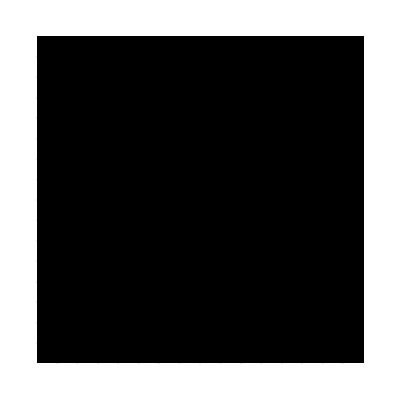

```mathematica
PlotDigit[x_]:=
Module[{scaleddata=-(x-Min[x])/(Max[x]-Min[x])},
ReliefPlot[Reverse[ArrayReshape[scaleddata,{16,16}]], Mesh->15,PlotTheme->"Monochrome",Frame->False,PlotRange->All]
]
PlotDigit[TrainingImages[[;;,553]]]
```

### Exercise 7.1a

Use the following code to enter your own digit. Note: make sure it uses the full grid (the top and bottom line should not be empty).
It makes the fields darker if you move ofter them (lighter if you toggle the pen color) and stores it in the variable img.
After creating a digit store it in myDigit using the command below.

```mathematica
img=ConstantArray[0,{256}];
values=Range[0,7]
colors=Blend[{White,Black},#]&/@(values/Max[values])
labels=#->" "&/@values
pixelValues=values/Max[values]*2-1
pencolor="Black"; 

Grid[{{
Text["Pen Color (click to change)"],Framed@Toggler[Dynamic[pencolor],{"Black"->" ","White"->" "},Background->Dynamic[ If[pencolor=="White",White,Black]], ImageSize->{30,30}]}}]
labels:=If[pencolor=="White",labels=#->" "&/@Reverse[values],labels=#->" "&/@values];
Grid[
Table[
Framed[
Dynamic[(* create a table of 16x16 Toggler elements, that increase or decrease the values, based on the Pen Color *)
If[pencolor=="White",
Toggler[
Dynamic[img[[#+1]]],Reverse[labels],
ImageSize->{15,15},ImageMargins->0,FrameMargins->0, AutoAction->Dynamic[img[[#+1]]≠labels[[1,1]] (* autoaction stops when it's white so it does not change to black *)
 ]
],
Toggler[
Dynamic[img[[#+1]]],labels, 
ImageSize->{15,15},ImageMargins->0,FrameMargins->0, AutoAction->Dynamic[img[[#+1]]≠labels[[Length[labels],1]] (* autoaction stops when it's black so it does not changeto white *)
 ]
]]],
FrameMargins->0,Background->Dynamic[ colors[[ img[[ #+1 ]]+1 ]] ]
]&[row*16+col],
{row,0,15},{col ,0,15}
] ,Spacings->{0,0}
]
```

{0,1,2,3,4,5,6,7}

{GrayLevel[1],GrayLevel[Rational[6, 7]],GrayLevel[Rational[5, 7]],GrayLevel[Rational[4, 7]],GrayLevel[Rational[3, 7]],GrayLevel[Rational[2, 7]],GrayLevel[Rational[1, 7]],GrayLevel[0]}

{0→ ,1→ ,2→ ,3→ ,4→ ,5→ ,6→ ,7→ }

{-1,-5/7,-3/7,-1/7,1/7,3/7,5/7,1}

Pen Color (click to change) |

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
{GrayLevel[1],GrayLevel[Rational[6, 7]],GrayLevel[Rational[5, 7]],GrayLevel[Rational[4, 7]],GrayLevel[Rational[3, 7]],GrayLevel[Rational[2, 7]],GrayLevel[Rational[1, 7]],GrayLevel[0]}
```

{GrayLevel[1],GrayLevel[Rational[6, 7]],GrayLevel[Rational[5, 7]],GrayLevel[Rational[4, 7]],GrayLevel[Rational[3, 7]],GrayLevel[Rational[2, 7]],GrayLevel[Rational[1, 7]],GrayLevel[0]}

### Exercise 7.1 b

After creating a digit store it in another variable myDigit (make sure the output is visible, so it can be executed again if necessary).

#### Answer

```mathematica
myDigit=img
```

{1,1,1,1,1,3,7,7,7,7,5,2,1,1,1,1,0,0,0,0,1,5,7,7,5,7,7,4,0,0,0,0,0,0,0,0,4,7,1,1,0,0,7,5,1,0,0,0,0,0,0,0,7,7,0,0,0,5,7,2,0,0,0,0,0,0,0,0,5,7,3,0,1,4,7,1,0,0,0,0,0,0,0,0,4,6,7,4,4,7,3,0,0,0,0,0,0,0,0,0,1,3,7,7,7,3,0,0,0,0,0,0,0,0,0,0,0,2,5,7,7,3,1,0,0,0,0,0,0,0,0,0,0,6,7,2,5,7,4,1,0,0,0,0,0,0,0,0,2,7,6,1,1,7,7,2,0,0,0,0,0,0,0,0,7,7,0,0,0,4,6,5,1,0,0,0,0,0,0,2,7,3,0,0,0,1,3,7,1,0,0,0,0,0,0,1,7,2,0,0,0,0,2,7,2,0,0,0,0,0,0,1,2,7,0,0,0,0,7,7,3,0,0,0,0,0,0,0,4,6,7,7,4,6,7,5,1,0,0,0,1,1,1,1,1,3,4,6,7,6,4,2,1,1,1,1}

### Exercise 7.1c

Now plot the image with the function PlotDigit, which should have been defined above .

#### Answer

```mathematica
PlotDigit[myDigit]
```

-Graphics-

### Exercise 7.2

To which picture in TrainingImages is this the closest ?
Hint: check out the Section Take the first image from the test set and find nearest known image. Instead of using the testimage, use myDigit.
Does the number match ? If not try to find a reason why (make sure the top and bottom line are not white). Does it look like digit that is closest ?

#### Answer

```mathematica
numberoftrainingimages=Dimensions[TrainingImages][[2]];
PlotDigit[myDigit]
alldistances=Table[Norm[TrainingImages[[;;,i]]-myDigit],{i,1,numberoftrainingimages}];
indexnearestknownimage=Ordering[alldistances,1];
PlotDigit[TrainingImages[[;;,indexnearestknownimage]]]
```

-Graphics-

-Graphics-

```mathematica
(* The image is recognized correctly. *)
```

### Exercise 7.3a

Extend the code to calculate the average three for all digits. Try to do this in a list.
Hint: a sorted list of all the unique labels can be obtained with Union[LabelsTrainingImages].

#### Answer

```mathematica
positionthrees=Flatten[Position[LabelsTrainingImages,3.]];
allthrees = TrainingImages[[;;,positionthrees]];
Dimensions[allthrees]
averagethree=Apply[Plus,allthrees,{1}]/Dimensions[allthrees][[2]];
PlotDigit[averagethree]
```

{256,131}

-Graphics-

```mathematica
averageDigits = Table[Apply[Plus, TrainingImages[[;;,Flatten[Position[LabelsTrainingImages,n]]]],{1}]/Dimensions[ TrainingImages[[;;,Flatten[Position[LabelsTrainingImages,n]]]]][[2]],{n,Union[LabelsTrainingImages]}];
PlotDigit[averageDigits[[2]]]
(*averageDigits[[i]] has the average of the digit i-1.*)
```

-Graphics-

### Exercise 7.3 b

To which of these average images is myDigit the closest?

#### Answer

```mathematica
allAverageDistances=Table[Norm[averageDigits[[i]]-myDigit],{i,1,10}];
indexNearestAverageimage=Ordering[allAverageDistances,1];
PlotDigit[averageDigits[[indexNearestAverageimage]]]
(*myDigit is closest the average of 8*)
```

-Graphics-

```mathematica
(**)
```

### Exercise 7.4

With Manipulate it is possible to generate interactive elements. The code below is an extension from the code from the recognize digits notebook, which makes it possible to select the digit to check against using the button.
Execute the code below and find out what the best match is (lowest norm). Write your findings in the text field below (what is the best match and is it correct; is there a close second ?)

#### Answer

```mathematica
Manipulate[Module[{labels,positions,allchars,U,S,V,Ur,relativeresidual},
labels=Union[LabelsTrainingImages];
positions=Flatten[Position[LabelsTrainingImages,labels[[pos+1]]]];
allchars= TrainingImages[[;;,positions]];
{U,S,V}=SingularValueDecomposition[allchars];
Ur:=U[[;;,Range[r]]];
Grid[{{PlotDigit[myDigit],
PlotDigit[Ur.Transpose[Ur].myDigit]},{"original",
{pos,relativeresidual=Norm[myDigit-Ur.Transpose[Ur].myDigit]/Norm[myDigit]}
}}]]
,{r,{5,10,15,20}},
{pos,0,9,1,ControlType->SetterBar},(* make sure pos (which digit to check against) can be selected with a bar *)
Initialization:>(r=10) (* start r at the default value of 10 *)
]
```

#### Comment:

The best match is: ...  for r=20

### Exercise 7.5a

Make a function that calculates the relativeresidual. You can use the function below (but change pos and myDigit to the parameters and make sure to assign a value to r).
Make a table that creates a list of relativeresidual values for all digits.

#### Answer

```mathematica
Clear[relativeresidual];
(*relativeresidual[digitTestNumber_,digitImage_]:=Module[{labels,positions,allchars,U,S,V,Ur,relativeresidual,r},
labels=Union[LabelsTrainingImages];
positions=Flatten[Position[LabelsTrainingImages,labels[[pos+1]]]];
allchars= TrainingImages[[;;,positions]];
{U,S,V}=SingularValueDecomposition[allchars];
Ur:=U[[;;,Range[r]]];
relativeresidual=Norm[myDigit-Ur.Transpose[Ur].myDigit]/Norm[myDigit]
]*)
relativeresidual[digitTestNumber_,digitImage_]:=Module[{labels,positions,allchars,U,S,V,Ur,relativeresidual},
labels=Union[LabelsTrainingImages];
positions=Flatten[Position[LabelsTrainingImages,labels[[digitTestNumber+1]]]];
allchars= TrainingImages[[;;,positions]];
{U,S,V}=SingularValueDecomposition[allchars];
Ur:=U[[;;,Range[20]]];
relativeresidual=Norm[digitImage-Ur.Transpose[Ur].digitImage]/Norm[digitImage]
]
tableOfRelativeResiduals = Table[relativeresidual[i,myDigit], {i,0,9}]
```

{0.562386,0.649661,0.607664,0.51784,0.636306,0.523969,0.586291,0.694757,0.491186,0.664278}

### Exercise 7.5b

Make a command to calculate the best match using singular value decomposition using the function generated in 7.5a

#### Answer

```mathematica
Clear[bestMatch]
bestMatch[myDigit_] := Module[{residuals},
residuals = Table[relativeresidual[i,myDigit], {i,Union[LabelsTestImages]}];
bestMatch = Position[residuals, Min[residuals]]-1]
bestMatch[myDigit]
```

{{8}}